# Polar coordinates

## 1. Polar and rectangular coordinates

```mathematica
polarToRectangular[r_,θ_]:={r Cos[θ],r Sin[θ]};
rectangularToPolar[x_,y_]:={Sqrt[(x^2)+(y^2)],ArcTan[y/x]};
```

### Problem 1.3

```mathematica
rectangularToPolar[2,3]
```

{√13,ArcTan[3/2]}

```mathematica
N[ArcTan[3/2]]
```

0.982794

### Problem 1.4

```mathematica
polarToRectangular[-Sqrt[13],ArcTan[3/2]+Pi]
```

{2,3}

### Problem 1.5

```mathematica
polarToRectangular[2,Pi/6]
```

### Problem 1.6

```mathematica
polarToRectangular[-4,Pi/3]
```

{-2,-2 √3}

### Problem 1.7

```mathematica
polarToRectangular[3,3 Pi/4]
```

{-3/(√2),3/(√2)}

## 2. Polar equation curves

### Problem 2.1

```mathematica
PolarPlot[2,{θ,0,2 Pi}]
```

### Problem 2.3

```mathematica
PolarPlot[2 Sin[θ],{θ,0,2 Pi}]
```

### Problem 2.5

```mathematica
PolarPlot[4 Cos[θ],{θ,0,2 Pi}]
```

### Problem 2.6

```mathematica
PolarPlot[Tan[θ] Sec[θ],{θ,0,2 Pi}]
```

### Problem 2.7

```mathematica
PolarPlot[6/(Sqrt[9-5 Sin[θ]^2]),{θ,0,2 Pi}]
```

### Problem 2.8

```mathematica
PolarPlot[-10 Cos[θ],{θ,0,2 Pi}]
```

### Problem 2.9

```mathematica
PolarPlot[6 (Sin[θ]+Cos[θ]),{θ,0,2 Pi}]
```

### Problem 2.10

```mathematica
PolarPlot[6 Sec[θ],{θ,0,2 Pi}]
```

## 4 Sketching curves

### Problem 4.1

```mathematica
theta=Table[a Pi/8,{a,0,16}]
```

{0,π/8,π/4,(3 π)/8,π/2,(5 π)/8,(3 π)/4,(7 π)/8,π,(9 π)/8,(5 π)/4,(11 π)/8,(3 π)/2,(13 π)/8,(7 π)/4,(15 π)/8,2 π}

```mathematica
AssociationThread[theta,N[1+Cos[theta]]]
```

<|0→2.,π/8→1.92388,π/4→1.70711,(3 π)/8→1.38268,π/2→1.,(5 π)/8→0.617317,(3 π)/4→0.292893,(7 π)/8→0.0761205,π→0.,(9 π)/8→0.0761205,(5 π)/4→0.292893,(11 π)/8→0.617317,(3 π)/2→1.,(13 π)/8→1.38268,(7 π)/4→1.70711,(15 π)/8→1.92388,2 π→2.|>

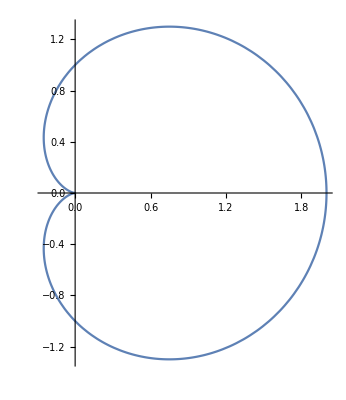

```mathematica
PolarPlot[1+Cos[θ],{θ,0,2 Pi}]
```

### Problem 4.2

```mathematica
AssociationThread[theta,N[1+2 Cos[theta]]]
```

<|0→3.,π/8→2.84776,π/4→2.41421,(3 π)/8→1.76537,π/2→1.,(5 π)/8→0.234633,(3 π)/4→-0.414214,(7 π)/8→-0.847759,π→-1.,(9 π)/8→-0.847759,(5 π)/4→-0.414214,(11 π)/8→0.234633,(3 π)/2→1.,(13 π)/8→1.76537,(7 π)/4→2.41421,(15 π)/8→2.84776,2 π→3.|>

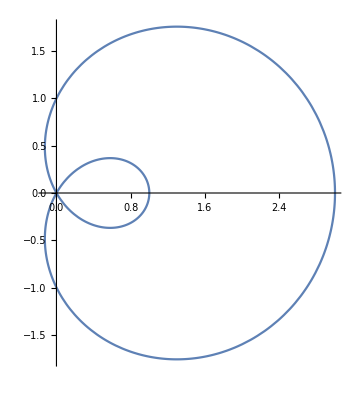

```mathematica
PolarPlot[1+2 Cos[θ],{θ,0,2 Pi}]
```